## Foreword, etc.

## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
(*Needs["Combinatorica`"]*)
```

### Test

```mathematica
nCollatz[9232]
```

{9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

### Transfer to PKG

```mathematica
nDP[f_, g_] := Function[a, DivisorSum[a, f[#] g[a/#] &]]
```

```mathematica
nPrimesLEqThan[n_]:=Prime[Range[PrimePi[n]]]
nPrimesBetween[n_,m_]:=Module[
{a1,a2,rng},
If[n<=m,a1=m;a2=n,a1=n;a2=m];
rng=Complement[nPrimesLEqThan[a1],nPrimesLEqThan[a2]];
rng]
nPrimesBetween[100,150]
```

{101,103,107,109,113,127,131,137,139,149}

## Topic

### Definition / Theorem

This is text.

#### Example

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2

## [ TBD: ] CONSTRUCTION OF THE INTEGERS

Notes:
a+d = b+c
(a+c, b+d)
(ac + bd, ad + bc )

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,98,111}]//tf
```

98 | -7
99 | 7
100 | -5/2
101 | 5/2
102 | -1/51
103 | 1/51
104 | -2/13
105 | 2/13
106 | -1/53
107 | 1/53
108 | -1/18
109 | 1/18
110 | -1/55
111 | 1/55

```mathematica
355./113
nQuotientToNatural[22/7]
nNaturalToQuotient[28481651]
```

3.14159

6777

355/113

```mathematica
FactorInteger[6776]
```

{{2,3},{7,1},{11,2}}

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,10000,10009}]
```

{{10000,-25/4},{10001,25/4},{10002,-1/5001},{10003,1/5001},{10004,-1/5002},{10005,1/5002},{10006,-1/5003},{10007,1/5003},{10008,-6/139},{10009,6/139}}

```mathematica
nQuotientToNatural[31/101]
nNaturalToQuotient[194123]
```

194123

31/101

```mathematica
nNaturalToQuotient[7901185]
```

1/123456

```mathematica
nQuotientToNatural[1/123456]
```

7901185

## tmp-1 ( Sum expression for Zeta(3) )

```mathematica
(-4 π^2)/7 Sum[Zeta[2k]/((2k+1)(2k+2)2^(2k)),{k,0,10}]//N
```

1.20206

```mathematica
Zeta[3]//N
```

1.20206

```mathematica
-4 π^2 Zeta'[-2]//N
```

1.20206

## nRandomLargePrimes

```mathematica
nDP[f_, g_] := Function[a, DivisorSum[a, f[#] g[a/#] &]]
```

```mathematica
Table[{k,nDP[2^PrimeNu[#]&,(-1)^PrimeOmega[#]&][k]},{k,1,12}]// tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1
11 | 1
12 | 1

```mathematica
nRandomLargePrimes={
1493681662543217878160621001493954482728761115029,
700739825495796892911470158595612191109099877292529,
1472096224144293702191366558640187434517863879629549,
2103773991264901723662580595147397654330635569039357,
2699243374499511472600789225180130783824859693484071,
398869148505334498610415829456039133740158757895987873,
549335317644366848620963598863612623797226033046822367,
1404331202801782850289552174866956170276744436689685661,
3193363039935965772365112697679561879002491633999044243,
16584481766395224445084325459256163383388354525876508557,
141219010751766643014541882207227887046904103493608636851,
308287092487477895094790383880763507229711563200387863779,
1400142646836180704088519408419116252818995710960172965243,
215108727189576815121508725751291721300023431942578921304283,
2158853164829929621820714762594477555397898278329482309747283,
20803237077583935736984609616651585718892273678491880706401153,
170192827244567637928627699850632238942014026794841802229591029,
22712761749503233807399473845700967947686275009367417295274790267,
670560185136141781047307957731270637430080412253382216571221454743,
33700436725730370103570399037732371300367702399100433767036365707703
};
nRandomLargePrimes//Length
```

20

```mathematica
Table[Length[IntegerDigits[k]],{k,nRandomLargePrimes}]
```

{49,51,52,52,52,54,54,55,55,56,57,57,58,60,61,62,63,65,66,68}

```mathematica
FactorInteger[10110310710911312713100000002003000001151061067069071073079083089097]
```

{{251,1},{1069,1},{55373,1},{59107,1},{3204048763,1},{111856839257,1},{126892254017,1},{253150816870736542139,1}}

```mathematica
FactorInteger[4520189026299330782353421687996961553+10^70+144^15+13]
```

{{2,1},{3,1},{5,1},{7,1},{11251,1},{395741,1},{6369875290950186450136086793,1},{1678988045311068808536988947913,1}}

## Arithmetical Functions

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2

```mathematica
2^6 3^6 5^1  7^1 11^1
Divisors[2^6 3^6 5^1  7^1 11^1]//Length
```

17962560

392

```mathematica
2^11 3^7 5^5  7^3 11^2
12 8 6 4 3
Divisors[2^11 3^7 5^5  7^3 11^2]//Length
```

580909190400000

6912

6912

```mathematica
2^13 3^11 5^7  7^5 11^3 13^2
14 12 8 6 4 3
Divisors[2^13 3^11 5^7  7^5 11^3 13^2]//Length
```

428616352408083840000000

96768

96768

```mathematica
96768/6912
```

14

```mathematica
l1:=Primes[2]
l2:={2,3,4}
target:={2^2,4^3,6^4}
```

## DirichletConvolve, DirichletTransform

```mathematica
2 Log[2]/Log[12]+Log[3]/Log[12]//N
```

1.

```mathematica
Log[2]/Log[30]+Log[3]/Log[30]+Log[5]/Log[30]//N
```

1.

```mathematica
f[k_]:=DirichletConvolve[1,EulerPhi[n],n,k]
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 2
3 | 3
4 | 4
5 | 5
6 | 6
7 | 7
8 | 8
9 | 9
10 | 10

```mathematica
f[k_]:=DirichletConvolve[1,MangoldtLambda[n],n,k]
f[k_]:=DirichletConvolve[1,MoebiusMu[n],n,k]
f[k_]:=DivisorSum[k,MoebiusMu[#]&]
Table[{k,-DivisorSum[k,MoebiusMu[#]Log[#]&]//Simplify,f[k]//Simplify},{k,1,10}]//tf;
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0

```mathematica
DirichletTransform[LiouvilleLambda[n],n,s]
DirichletTransform[MangoldtLambda[n],n,s]
```

Zeta[2 s]/Zeta[s]

-Zeta'[s]/Zeta[s]

## Ontbinding f[n_]:=1

```mathematica
f[n_]:=1
Table[{n,f[n]},{n,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

```mathematica
g[n_]:=nDP[2^PrimeNu[#]&,(-1)^PrimeOmega[#]&][n]
Table[{n,g[n]},{n,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

## Averages of Arithmetical Functions

## Theorems

## “Bakjes” R&D

## Study Bellman

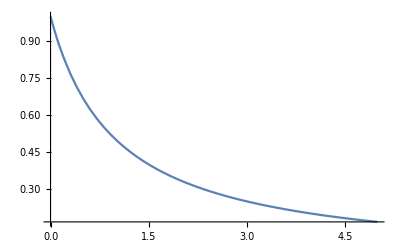

```mathematica
f[x_]:=1/(x+1)
Plot[f[x],{x,0,5}]
```

```mathematica
{Sum[f[k],{k,1,5}],Integrate[f[s],{s,0,5}],Sum[f[k],{k,0,4}]}//N
```

{1.45,1.79176,2.28333}

```mathematica
g[n_]:=Module[{v},If[n==2,
v="A",
If[n==3,
v="B",
v="Neither"
];
];
v
]/;IntegerQ[n]
```

## (* ERROR: - Enumerator for p q r - Dev - BUG *)

```mathematica
enumpq[n_]:=Module[{k=0,lst={}},
For[i=1,i<=n,i++,
For[j=1,j<i,j++,
k++;
lst=Append[lst,Prime[i]*Prime[j]];
];
];
lst
];
```

```mathematica
Select[enumpq[15],#<=100&]
```

{6,10,15,14,21,35,22,33,55,77,26,39,65,91,34,51,85,38,57,95,46,69,58,87,62,93,74,82,86,94}

```mathematica
enumpqr[n_]:=Module[{k=0,lst={}},
For[i=3,i<=n,i++,
For[j=1,j<=Prime[i],j++,
If[Mod[enumpq[[j]],Prime[i]]==0,Break[]];
k++;
Print[{k,l11[[j]]Prime[i]}];
];
]
]
```

## Bakjes-Info-[TBD]

```mathematica
viaPrt[n_]:=Flatten[Map[IntegerPartitions[#]&,Range[n]],1]
viaNum[n_]:=Module[{ls},
lst={};
For[i=2,i<n,i++,
lst=Append[lst,FactorInteger[i][[All,2]]]
];
Sort[DeleteDuplicates[DeleteDuplicates[lst,Sort[#1]==Sort[#2]&]]]
]

viaNum2[n_]:=Module[{ls},
lst={{0}};
For[i=2,i<(n+1),i++,
lst=Append[lst,Reverse[Sort[FactorInteger[i][[All,2]]]]]
];
lst
]

viaNum3[n_]:=Module[{ls},
lst={{0 ,{0}}};
For[i=2,i<(n+1),i++,
	lst=Append[lst,{Reverse[Sort[FactorInteger[i][[All,2]]]]}
]
];
lst
]
```

## Experiments: container (“Bakjes”) size

### Code to Transfer to Number Theory Package

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc},
assoc=<|{0}->{1}|>;
If[
MissingQ[Lookup[assoc,{nGetPrimeSignature[#]}][[1]]],
assoc=AssociateTo[assoc,nGetPrimeSignature[#]->{#}],
assoc=AssociateTo[assoc,nGetPrimeSignature[#]->Append[Key[nGetPrimeSignature[#]][assoc],#]] 
]&/@Range[2,n];
assoc
]
```

### Alpha Tests

```mathematica
ds=nBuildPrimeSignatureContainers[100]//Dataset;
Normal[Values[KeySelect[ds,#=={1,1,1}&]]][[1]]//FactorInteger
```

{{{2,1},{3,1},{5,1}},{{2,1},{3,1},{7,1}},{{2,1},{3,1},{11,1}},{{2,1},{5,1},{7,1}},{{2,1},{3,1},{13,1}}}

### Building Subtrees

```mathematica
Prime[Range[PrimePi[10]]]
Normal[Values[KeySelect[ds,#=={1,1}&]]]
```

{2,3,5,7}

{{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}}

```mathematica
ls=(KeySelect[ds,#=={1,1}&]//Values//Normal)[[1]]

ls2=Select[ls,Not[Divisible[#,2]]&];
Complement[ls,ls2]

ls3=Select[ls2,Not[Divisible[#,3]]&];
Complement[ls2,ls3]

ls5=Select[ls3,Not[Divisible[#,5]]&];
Complement[ls3,ls5]

ls7=Select[ls5,Not[Divisible[#,7]]&];
Complement[ls5,ls7]

Union[ls,ls2,ls3,ls5,ls7]
FactorInteger[Union[ls,ls2,ls3,ls5,ls7]]
```

{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}

{6,10,14,22,26,34,38,46,58,62,74,82,86,94}

{15,21,33,39,51,57,69,87,93}

{35,55,65,85,95}

{77,91}

{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}

{{{2,1},{3,1}},{{2,1},{5,1}},{{2,1},{7,1}},{{3,1},{5,1}},{{3,1},{7,1}},{{2,1},{11,1}},{{2,1},{13,1}},{{3,1},{11,1}},{{2,1},{17,1}},{{5,1},{7,1}},{{2,1},{19,1}},{{3,1},{13,1}},{{2,1},{23,1}},{{3,1},{17,1}},{{5,1},{11,1}},{{3,1},{19,1}},{{2,1},{29,1}},{{2,1},{31,1}},{{5,1},{13,1}},{{3,1},{23,1}},{{2,1},{37,1}},{{7,1},{11,1}},{{2,1},{41,1}},{{5,1},{17,1}},{{2,1},{43,1}},{{3,1},{29,1}},{{7,1},{13,1}},{{3,1},{31,1}},{{2,1},{47,1}},{{5,1},{19,1}}}

## “Bakjes” R&D Devs

## Prototype-1 ( Without prsig={1,1} )

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc,k,prsig,m},

assoc=<|{0}->{1}|>;
For[k=2,k<=n,k++,
prsig=nGetPrimeSignature[k];
If[
MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]] ;
];
];
assoc
]                                                                                                                                                                                                                                              

nBuildPrimeSignatureContainers[31]
```

<|{0}→{1},{1}→{2,3,5,7,11,13,17,19,23,29,31},{2}→{4,9,25},{1,1}→{6,10,14,15,21,22,26},{3}→{8,27},{1,2}→{12,18,20,28},{4}→{16},{1,3}→{24},{1,1,1}→{30}|>

## Prototype-2: ( Without prsig = {1,1,1, ...} ) /* Code likely NOT optimal / efficient */

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc,k,prsig,m},
assoc=<|{0}->{1}|>;

For[k=2,k<=n,k++,
prsig=nGetPrimeSignature[k];
m=Sort[FactorInteger[k][[All,1]]][[1]];
If[prsig=={1,1},
If[MissingQ[assoc[[Key[prsig]]]],
assoc=Association[assoc,prsig-><|{m,"p"}->{k}|>];,
If[MissingQ[assoc[prsig][{m,"p"}]],
assoc[prsig]=Association[Key[prsig][assoc],{m,"p"}->{k}],
AppendTo[assoc[prsig][{m,"p"}],k];
];
];,
If[MissingQ[assoc[[Key[prsig]]]],
assoc=Association[assoc,prsig->{k}],
AppendTo[assoc[[Key[prsig]]],k]];
];
];
assoc
]
```

### Demonstrations / Test-runs

```mathematica
data=Timing[nBuildPrimeSignatureContainers[18]]
```

{0.,<|{0}→{1},{1}→{2,3,5,7,11,13,17},{2}→{4,9},{1,1}→<|{2,p}→{6,10,14},{3,p}→{15}|>,{3}→{8},{1,2}→{12,18},{4}→{16}|>}

```mathematica
data//Dataset
```

### Other subject---

```mathematica
Table[StirlingS2[n,k],{n,0,12},{k,0,n}]//tf
```

1 |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 1 |  |  |  |  |  |  |  |  |  | 
0 | 1 | 3 | 1 |  |  |  |  |  |  |  |  | 
0 | 1 | 7 | 6 | 1 |  |  |  |  |  |  |  | 
0 | 1 | 15 | 25 | 10 | 1 |  |  |  |  |  |  | 
0 | 1 | 31 | 90 | 65 | 15 | 1 |  |  |  |  |  | 
0 | 1 | 63 | 301 | 350 | 140 | 21 | 1 |  |  |  |  | 
0 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 |  |  |  | 
0 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 |  |  | 
0 | 1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1 |  | 
0 | 1 | 1023 | 28501 | 145750 | 246730 | 179487 | 63987 | 11880 | 1155 | 55 | 1 | 
0 | 1 | 2047 | 86526 | 611501 | 1379400 | 1323652 | 627396 | 159027 | 22275 | 1705 | 66 | 1

```mathematica
IntegerName[1000000,{"Dutch"}]
IntegerName[1000000000,{"Dutch"}]
IntegerName[1000000000000,{"Dutch"}]
IntegerName[1000000000000000,{"Dutch"}]

IntegerName[1000000]
IntegerName[1000000000]
IntegerName[1000000000000]
IntegerName[1000000000000000]
```

een miljoen

een miljard

een biljoen

een biljard

1 million

1 billion

1 trillion

1 quadrillion

```mathematica
X={a,b,c}
```

{a,b,c}

```mathematica
nGetPrimeSignature[100]
```

{2,2}

```mathematica
FactorInteger[100]
```

{{2,2},{5,2}}

```mathematica
Y={2,2,5,5};
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]
```

{{{2,2,5,5}},{{2},{2,5,5}},{{2,2},{5,5}},{{5},{2,2,5}},{{2,5},{2,5}},{{2},{2},{5,5}},{{2},{5},{2,5}},{{5},{5},{2,2}},{{2},{2},{5},{5}}}

```mathematica
Array[2&,2]
```

{2,2}

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
f[{2,3}]
f[{3,2}]
```

{2,2,2}

{3,3}

```mathematica
Y=Flatten[Append[Append[f[{2,3}],f[{3,1}]],f[{5,1}]]]
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]//Length
```

{2,2,2,3,5}

21

```mathematica
Join[{1},{3,3,4},{5}]
```

{1,3,3,4,5}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[96]]//Flatten
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]//Length
Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]]
```

{f[{2,5}],f[{3,1}]}

2

{{{f[{2,5}],f[{3,1}]}},{{f[{2,5}]},{f[{3,1}]}}}

```mathematica
lst={
{{2,2,2,2,2,3}},
{{2},{2,2,2,2,3}},
{{2,2},{2,2,2,3}},
{{2,2,2},{2,2,3}},
{{2,3},{2,2,2,2}},
{{3},{2,2,2,2,2}},
{{2},{2},{2,2,2,3}},
{{2},{2,2},{2,2,3}},
{{2},{2,3},{2,2,2}},
{{2},{3},{2,2,2,2}},
{{2,2},{2,2},{2,3}},
{{3},{2,2},{2,2,2}},{{2},{2},{2},{2,2,3}},{{2},{2},{2,2},{2,3}},{{2},{2},{3},{2,2,2}},{{2},{3},{2,2},{2,2}},{{2},{2},{2},{2},{2,3}},{{2},{2},{2},{3},{2,2}},{{2},{2},{2},{2},{2},{3}}};
```

```mathematica
Map[Apply[Times,#]&,lst,{2}]//tf
```

96 |  |  |  |  | 
2 | 48 |  |  |  | 
4 | 24 |  |  |  | 
8 | 12 |  |  |  | 
6 | 16 |  |  |  | 
3 | 32 |  |  |  | 
2 | 2 | 24 |  |  | 
2 | 4 | 12 |  |  | 
2 | 6 | 8 |  |  | 
2 | 3 | 16 |  |  | 
4 | 4 | 6 |  |  | 
3 | 4 | 8 |  |  | 
2 | 2 | 2 | 12 |  | 
2 | 2 | 4 | 6 |  | 
2 | 2 | 3 | 8 |  | 
2 | 3 | 4 | 4 |  | 
2 | 2 | 2 | 2 | 6 | 
2 | 2 | 2 | 3 | 4 | 
2 | 2 | 2 | 2 | 2 | 3

```mathematica
Apply[Times,{2,3,4}]
```

24

```mathematica
FactorInteger[420]
```

{{2,2},{3,1},{5,1},{7,1}}

```mathematica
(* iets met Function *)
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//tf
```

{2,2,3,3}

9

{{36},{2,18},{4,9},{3,12},{6,6},{2,2,9},{2,3,6},{3,3,4},{2,2,3,3}}

36 |  |  | 
2 | 18 |  | 
4 | 9 |  | 
3 | 12 |  | 
6 | 6 |  | 
2 | 2 | 9 | 
2 | 3 | 6 | 
3 | 3 | 4 | 
2 | 2 | 3 | 3

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//tf
```

{2,2,2,3,3}

16

{{72},{2,36},{4,18},{9,8},{3,24},{6,12},{2,2,18},{2,4,9},{2,3,12},{2,6,6},{3,4,6},{3,3,8},{2,2,2,9},{2,2,3,6},{2,3,3,4},{2,2,2,3,3}}

72 |  |  |  | 
2 | 36 |  |  | 
4 | 18 |  |  | 
9 | 8 |  |  | 
3 | 24 |  |  | 
6 | 12 |  |  | 
2 | 2 | 18 |  | 
2 | 4 | 9 |  | 
2 | 3 | 12 |  | 
2 | 6 | 6 |  | 
3 | 4 | 6 |  | 
3 | 3 | 8 |  | 
2 | 2 | 2 | 9 | 
2 | 2 | 3 | 6 | 
2 | 3 | 3 | 4 | 
2 | 2 | 2 | 3 | 3

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 3 3 ]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,3,3}

{{18},{2,9},{3,6},{2,3,3}}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[6]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,3}

{{6},{2,3}}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[12]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,2,3}

{{12},{2,6},{3,4},{2,2,3}}

### tmp

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
```

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
```

```mathematica
Flatten[Map[Function[x,Array[x[[1]]&,x [[2]]]],FactorInteger[72]]]
```

{{2,2,2},{3,3}}

```mathematica
nFactorListInteger[n_]:=Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Flatten[Map[Function[x,Array[x[[1]]&,x [[2]]]],FactorInteger[n]]]]]]],{2}]
```

```mathematica
lst=nFactorListInteger[10000]//Length
```

109

```mathematica
Table[StirlingS2[n,k],{n,0,6},{k,0,n}]//tf
```

1 |  |  |  |  |  | 
0 | 1 |  |  |  |  | 
0 | 1 | 1 |  |  |  | 
0 | 1 | 3 | 1 |  |  | 
0 | 1 | 7 | 6 | 1 |  | 
0 | 1 | 15 | 25 | 10 | 1 | 
0 | 1 | 31 | 90 | 65 | 15 | 1

```mathematica
PartitionsP[4]
```

5

```mathematica
BellB[4]
```

15

```mathematica
117 17
```

1989

```mathematica
nFactorListInteger[30]//tf
```

30 |  | 
2 | 15 | 
5 | 6 | 
3 | 10 | 
2 | 3 | 5

```mathematica
Solve[2^x (2y+1)==z&& x>0&&y>0&&z>0&&x==3&&z>0&&z<=48,{y,z},Integers]
```

{{y→ConditionalExpression[1, x==3],z→ConditionalExpression[24, x==3]},{y→ConditionalExpression[2, x==3],z→ConditionalExpression[40, x==3]}}

## Prepare nFactorListInteger => Number Theory Package

```mathematica
nFactorListIntegerDEV[n_]:=Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Flatten[Map[Function[x,Array[x[[1]]&,x [[2]]]],FactorInteger[n]]]]]]],{2}]
```

## TEMP

```mathematica
IntegerPartitions[5]//Length
IntegerPartitions[4]//Length
IntegerPartitions[3]//Length
IntegerPartitions[0]//Length
IntegerPartitions[-2]//Length
```

7

5

3

1

0

```mathematica
PartitionsP[5]
PartitionsP[4]
PartitionsP[3]
PartitionsP[0]
PartitionsP[-2]
```

7

5

3

1

0

```mathematica
Series[Product[1/(1-x^n),{n,1,Infinity}],{x,0,12}]
Series[Product[1/(1-x^(2n-1)),{n,1,Infinity}],{x,0,12}]
Series[1/(1-x^(2 2-1)),{x,0,10}]
```

1+x+2 x^2+3 x^3+5 x^4+7 x^5+11 x^6+15 x^7+22 x^8+30 x^9+42 x^10+56 x^11+77 x^12+O[x]^13

1+x+x^2+2 x^3+2 x^4+3 x^5+4 x^6+5 x^7+6 x^8+8 x^9+10 x^10+12 x^11+15 x^12+O[x]^13

1+x^3+x^6+x^9+O[x]^11

```mathematica
Map[Total[Select[#,OddQ]]&,IntegerPartitions[10]]
```

{0,10,0,2,10,8,10,0,4,0,2,4,10,6,8,10,6,8,10,0,2,6,4,6,0,2,4,6,10,6,8,10,4,6,8,10,0,2,4,6,8,10}

```mathematica
Select[Map[Apply[And,#]&,Map[OddQ[#]&,IntegerPartitions[12]]],#==True&]//Length
```

15

```mathematica
Expand[(1+x+x^2+x^3)(1+x^3)]
```

1+x+x^2+2 x^3+x^4+x^5+x^6

```mathematica
Series[1/(1-x^5),{x,0,10}]//Normal
```

1+x^5+x^10

```mathematica
(1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10)(1+x^2+x^4+x^6+x^8+x^10)(1+x^3+x^6+x^9)(1+x^4+x^8)(1+x^5+x^10)(1+x^6)(1+x^7)(1+x^8)(1+x^9)(1+x^10)//Expand
```

1+x+2 x^2+3 x^3+5 x^4+7 x^5+11 x^6+15 x^7+22 x^8+30 x^9+42 x^10+54 x^11+70 x^12+91 x^13+116 x^14+145 x^15+181 x^16+222 x^17+270 x^18+325 x^19+386 x^20+454 x^21+529 x^22+616 x^23+707 x^24+805 x^25+910 x^26+1022 x^27+1135 x^28+1255 x^29+1374 x^30+1497 x^31+1618 x^32+1741 x^33+1856 x^34+1966 x^35+2069 x^36+2165 x^37+2246 x^38+2319 x^39+2379 x^40+2425 x^41+2456 x^42+2473 x^43+2473 x^44+2456 x^45+2425 x^46+2379 x^47+2319 x^48+2246 x^49+2165 x^50+2069 x^51+1966 x^52+1856 x^53+1741 x^54+1618 x^55+1497 x^56+1374 x^57+1255 x^58+1135 x^59+1022 x^60+910 x^61+805 x^62+707 x^63+616 x^64+529 x^65+454 x^66+386 x^67+325 x^68+270 x^69+222 x^70+181 x^71+145 x^72+116 x^73+91 x^74+70 x^75+54 x^76+42 x^77+30 x^78+22 x^79+15 x^80+11 x^81+7 x^82+5 x^83+3 x^84+2 x^85+x^86+x^87

```mathematica
(1+x+x^2+x^3+x^4+x^5)(1+x^2+x^4)(1+x^3)(1+x^4)(1+x^5)//Expand
```

1+x+2 x^2+3 x^3+5 x^4+7 x^5+7 x^6+10 x^7+11 x^8+13 x^9+12 x^10+12 x^11+13 x^12+11 x^13+10 x^14+7 x^15+7 x^16+5 x^17+3 x^18+2 x^19+x^20+x^21

```mathematica
√2+√3-Pi//N
22/7.-Pi
355/113.-Pi
```

0.00467172

0.00126449

2.66764×10^-7

```mathematica
355/113.
```

3.14159

```mathematica
CoefficientList[Normal[Series[Product[1-x^n,{n,1,Infinity}],{x,0,100}]],x]
```

{1,-1,-1,0,0,1,0,1,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1}

```mathematica
Table[{k,DivisorSigma[1,k]},{k,1,20}]//tf
```

1 | 1
2 | 3
3 | 4
4 | 7
5 | 6
6 | 12
7 | 8
8 | 15
9 | 13
10 | 18
11 | 12
12 | 28
13 | 14
14 | 24
15 | 24
16 | 31
17 | 18
18 | 39
19 | 20
20 | 42

```mathematica
355/113.
```

3.14159

```mathematica
Normal[Series[Product[1-x^n,{n,1,Infinity}],{x,0,100}]]
```

1-x-x^2+x^5+x^7-x^12-x^15+x^22+x^26-x^35-x^40+x^51+x^57-x^70-x^77+x^92+x^100

```mathematica
t[n_]:=Table[(-1)^m(x^(m/2(3m-1))+x^(m/2(3m+1))),{m,1,n}]
1+Apply[Plus,t[10]]
```

1-x-x^2+x^5+x^7-x^12-x^15+x^22+x^26-x^35-x^40+x^51+x^57-x^70-x^77+x^92+x^100-x^117-x^126+x^145+x^155

```mathematica
(40000./50)/300
```

2.66667

```mathematica
Normal[Series[Product[1+x^(2^k),{k,0,Infinity}],{x,0,10}]]
```

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10

```mathematica
Product[1+x^(2^k),{k,0,Infinity}]
```

1/(1-x)

```mathematica
IntegerPartitions[10,{3}]//tf
Select[IntegerPartitions[10],#[[1]]==3&]//tf
```

8 | 1 | 1
7 | 2 | 1
6 | 3 | 1
6 | 2 | 2
5 | 4 | 1
5 | 3 | 2
4 | 4 | 2
4 | 3 | 3

3 | 3 | 3 | 1 |  |  |  | 
3 | 3 | 2 | 2 |  |  |  | 
3 | 3 | 2 | 1 | 1 |  |  | 
3 | 3 | 1 | 1 | 1 | 1 |  | 
3 | 2 | 2 | 2 | 1 |  |  | 
3 | 2 | 2 | 1 | 1 | 1 |  | 
3 | 2 | 1 | 1 | 1 | 1 | 1 | 
3 | 1 | 1 | 1 | 1 | 1 | 1 | 1

```mathematica
CoefficientList[Normal[Series[1/(1-x^41)1/(1-x^31)1/(1-x^21)1/(1-x^11)1/(1-x^1),{x,0,41}]],x][[41+1]]
```

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+2 x^11+2 x^12+2 x^13+2 x^14+2 x^15+2 x^16+2 x^17+2 x^18+2 x^19+2 x^20+3 x^21+4 x^22+4 x^23+4 x^24+4 x^25+4 x^26+4 x^27+4 x^28+4 x^29+4 x^30+5 x^31+6 x^32+7 x^33+7 x^34+7 x^35+7 x^36+7 x^37+7 x^38+7 x^39+7 x^40+8 x^41

8

```mathematica
CoefficientList[Normal[Series[1/(1-x^5)1/(1-x^10)1/(1-x^50)1/(1-x^100)1/(1-x^200),{x,0,1001}]],x][[50+1]]
```

7

```mathematica
Series[Product[1/(1-x^k),{k,1,Infinity}],{x,0,10}]
Series[Product[1-x^k,{k,1,Infinity}],{x,0,350}]
```

1+x+2 x^2+3 x^3+5 x^4+7 x^5+11 x^6+15 x^7+22 x^8+30 x^9+42 x^10+O[x]^11

1-x-x^2+x^5+x^7-x^12-x^15+x^22+x^26-x^35-x^40+x^51+x^57-x^70-x^77+x^92+x^100-x^117-x^126+x^145+x^155-x^176-x^187+x^210+x^222-x^247-x^260+x^287+x^301-x^330-x^345+O[x]^351

```mathematica
t[n_]:=n/2(3n+1)
Table[t[k],{k,1,15}]//tf
```

2
7
15
26
40
57
77
100
126
155
187
222
260
301
345

```mathematica
(1-x)(1-x^2)(1-x^3)(1-x^4)(1-x^5)(1-x^6)(1-x^7)(1-x^8)(1-x^9)(1-x^10)(1-x^11)(1-x^12)//Expand
```

1-x-x^2+x^5+x^7-x^12+x^13-2 x^15-x^16-x^17+x^20+x^21+2 x^22+x^23+x^24+2 x^26-x^28-2 x^29-2 x^30-2 x^31-2 x^32-x^33-x^34+x^36+2 x^37+x^38+4 x^39+x^40+2 x^41+x^42-x^44-x^45-2 x^46-2 x^47-2 x^48-2 x^49-x^50+2 x^52+x^54+x^55+2 x^56+x^57+x^58-x^61-x^62-2 x^63+x^65-x^66+x^71+x^73-x^76-x^77+x^78

```mathematica
IntegerName[123456789]
```

123 million 456 thousand 789

```mathematica
p1=Product[1-x^k,{k,1,20}]//Expand//Normal
p2=Series[Product[1/(1-x^k),{k,1,Infinity}],{x,0,25}]//Normal;
p1 p2 //Expand;
```

1-x-x^2+x^5+x^7-x^12-x^15+x^21+x^22-x^23-x^24-x^25+x^26+x^28+x^29+x^30+x^31+x^32-x^35-x^36-x^37-x^38-x^39-2 x^40-x^41-x^45-x^46+x^49+x^50+3 x^51+2 x^52+3 x^53+2 x^54+3 x^55+x^56+2 x^57-x^60-2 x^61-3 x^62-2 x^63-3 x^64-3 x^65-3 x^66-4 x^67-3 x^68-3 x^69-3 x^70-2 x^71+x^72+x^73+3 x^74+3 x^75+5 x^76+3 x^77+6 x^78+5 x^79+6 x^80+4 x^81+4 x^82+2 x^83+2 x^84-x^86-3 x^87-3 x^88-5 x^89-6 x^90-7 x^91-6 x^92-7 x^93-6 x^94-4 x^95-4 x^96-x^97-2 x^98+x^99+3 x^100+5 x^101+4 x^102+7 x^103+6 x^104+8 x^105+6 x^106+7 x^107+4 x^108+5 x^109+3 x^110+x^111-2 x^112-x^113-4 x^114-4 x^115-6 x^116-7 x^117-6 x^118-7 x^119-6 x^120-5 x^121-3 x^122-3 x^123-x^124+2 x^126+2 x^127+4 x^128+4 x^129+6 x^130+5 x^131+6 x^132+3 x^133+5 x^134+3 x^135+3 x^136+x^137+x^138-2 x^139-3 x^140-3 x^141-3 x^142-4 x^143-3 x^144-3 x^145-3 x^146-2 x^147-3 x^148-2 x^149-x^150+2 x^153+x^154+3 x^155+2 x^156+3 x^157+2 x^158+3 x^159+x^160+x^161-x^164-x^165-x^169-2 x^170-x^171-x^172-x^173-x^174-x^175+x^178+x^179+x^180+x^181+x^182+x^184-x^185-x^186-x^187+x^188+x^189-x^195-x^198+x^203+x^205-x^208-x^209+x^210

```mathematica
p1
CoefficientList[p1,x][[1;;10]]
```

1-x-x^2+x^5+x^7-x^12-x^15+x^21+x^22-x^23-x^24-x^25+x^26+x^28+x^29+x^30+x^31+x^32-x^35-x^36-x^37-x^38-x^39-2 x^40-x^41-x^45-x^46+x^49+x^50+3 x^51+2 x^52+3 x^53+2 x^54+3 x^55+x^56+2 x^57-x^60-2 x^61-3 x^62-2 x^63-3 x^64-3 x^65-3 x^66-4 x^67-3 x^68-3 x^69-3 x^70-2 x^71+x^72+x^73+3 x^74+3 x^75+5 x^76+3 x^77+6 x^78+5 x^79+6 x^80+4 x^81+4 x^82+2 x^83+2 x^84-x^86-3 x^87-3 x^88-5 x^89-6 x^90-7 x^91-6 x^92-7 x^93-6 x^94-4 x^95-4 x^96-x^97-2 x^98+x^99+3 x^100+5 x^101+4 x^102+7 x^103+6 x^104+8 x^105+6 x^106+7 x^107+4 x^108+5 x^109+3 x^110+x^111-2 x^112-x^113-4 x^114-4 x^115-6 x^116-7 x^117-6 x^118-7 x^119-6 x^120-5 x^121-3 x^122-3 x^123-x^124+2 x^126+2 x^127+4 x^128+4 x^129+6 x^130+5 x^131+6 x^132+3 x^133+5 x^134+3 x^135+3 x^136+x^137+x^138-2 x^139-3 x^140-3 x^141-3 x^142-4 x^143-3 x^144-3 x^145-3 x^146-2 x^147-3 x^148-2 x^149-x^150+2 x^153+x^154+3 x^155+2 x^156+3 x^157+2 x^158+3 x^159+x^160+x^161-x^164-x^165-x^169-2 x^170-x^171-x^172-x^173-x^174-x^175+x^178+x^179+x^180+x^181+x^182+x^184-x^185-x^186-x^187+x^188+x^189-x^195-x^198+x^203+x^205-x^208-x^209+x^210

{1,-1,-1,0,0,1,0,1,0,0}

```mathematica
q1=CoefficientRules[p1,x]//Reverse;
```

```mathematica
Map[{x #[[1,1]]#[[2]]}&,q1]
```

{{0},{-x},{-2 x},{5 x},{7 x},{-12 x},{-15 x},{21 x},{22 x},{-23 x},{-24 x},{-25 x},{26 x},{28 x},{29 x},{30 x},{31 x},{32 x},{-35 x},{-36 x},{-37 x},{-38 x},{-39 x},{-80 x},{-41 x},{-45 x},{-46 x},{49 x},{50 x},{153 x},{104 x},{159 x},{108 x},{165 x},{56 x},{114 x},{-60 x},{-122 x},{-186 x},{-126 x},{-192 x},{-195 x},{-198 x},{-268 x},{-204 x},{-207 x},{-210 x},{-142 x},{72 x},{73 x},{222 x},{225 x},{380 x},{231 x},{468 x},{395 x},{480 x},{324 x},{328 x},{166 x},{168 x},{-86 x},{-261 x},{-264 x},{-445 x},{-540 x},{-637 x},{-552 x},{-651 x},{-564 x},{-380 x},{-384 x},{-97 x},{-196 x},{99 x},{300 x},{505 x},{408 x},{721 x},{624 x},{840 x},{636 x},{749 x},{432 x},{545 x},{330 x},{111 x},{-224 x},{-113 x},{-456 x},{-460 x},{-696 x},{-819 x},{-708 x},{-833 x},{-720 x},{-605 x},{-366 x},{-369 x},{-124 x},{252 x},{254 x},{512 x},{516 x},{780 x},{655 x},{792 x},{399 x},{670 x},{405 x},{408 x},{137 x},{138 x},{-278 x},{-420 x},{-423 x},{-426 x},{-572 x},{-432 x},{-435 x},{-438 x},{-294 x},{-444 x},{-298 x},{-150 x},{306 x},{154 x},{465 x},{312 x},{471 x},{316 x},{477 x},{160 x},{161 x},{-164 x},{-165 x},{-169 x},{-340 x},{-171 x},{-172 x},{-173 x},{-174 x},{-175 x},{178 x},{179 x},{180 x},{181 x},{182 x},{184 x},{-185 x},{-186 x},{-187 x},{188 x},{189 x},{-195 x},{-198 x},{203 x},{205 x},{-208 x},{-209 x},{210 x}}

```mathematica
q1
```

{{0}→1,{1}→-1,{2}→-1,{5}→1,{7}→1,{12}→-1,{15}→-1,{21}→1,{22}→1,{23}→-1,{24}→-1,{25}→-1,{26}→1,{28}→1,{29}→1,{30}→1,{31}→1,{32}→1,{35}→-1,{36}→-1,{37}→-1,{38}→-1,{39}→-1,{40}→-2,{41}→-1,{45}→-1,{46}→-1,{49}→1,{50}→1,{51}→3,{52}→2,{53}→3,{54}→2,{55}→3,{56}→1,{57}→2,{60}→-1,{61}→-2,{62}→-3,{63}→-2,{64}→-3,{65}→-3,{66}→-3,{67}→-4,{68}→-3,{69}→-3,{70}→-3,{71}→-2,{72}→1,{73}→1,{74}→3,{75}→3,{76}→5,{77}→3,{78}→6,{79}→5,{80}→6,{81}→4,{82}→4,{83}→2,{84}→2,{86}→-1,{87}→-3,{88}→-3,{89}→-5,{90}→-6,{91}→-7,{92}→-6,{93}→-7,{94}→-6,{95}→-4,{96}→-4,{97}→-1,{98}→-2,{99}→1,{100}→3,{101}→5,{102}→4,{103}→7,{104}→6,{105}→8,{106}→6,{107}→7,{108}→4,{109}→5,{110}→3,{111}→1,{112}→-2,{113}→-1,{114}→-4,{115}→-4,{116}→-6,{117}→-7,{118}→-6,{119}→-7,{120}→-6,{121}→-5,{122}→-3,{123}→-3,{124}→-1,{126}→2,{127}→2,{128}→4,{129}→4,{130}→6,{131}→5,{132}→6,{133}→3,{134}→5,{135}→3,{136}→3,{137}→1,{138}→1,{139}→-2,{140}→-3,{141}→-3,{142}→-3,{143}→-4,{144}→-3,{145}→-3,{146}→-3,{147}→-2,{148}→-3,{149}→-2,{150}→-1,{153}→2,{154}→1,{155}→3,{156}→2,{157}→3,{158}→2,{159}→3,{160}→1,{161}→1,{164}→-1,{165}→-1,{169}→-1,{170}→-2,{171}→-1,{172}→-1,{173}→-1,{174}→-1,{175}→-1,{178}→1,{179}→1,{180}→1,{181}→1,{182}→1,{184}→1,{185}→-1,{186}→-1,{187}→-1,{188}→1,{189}→1,{195}→-1,{198}→-1,{203}→1,{205}→1,{208}→-1,{209}→-1,{210}→1}

```mathematica
10^6/64
```

15625

```mathematica
5./7  42
```

30.

## TEMP-1

```mathematica
Series[1/(1-2x),{x,0,15}]//Normal
```

1+2 x+4 x^2+8 x^3+16 x^4+32 x^5+64 x^6+128 x^7+256 x^8+512 x^9+1024 x^10+2048 x^11+4096 x^12+8192 x^13+16384 x^14+32768 x^15

```mathematica
Series[1/(1-x-x^2),{x,0,10}]//Normal
```

1+x+2 x^2+3 x^3+5 x^4+8 x^5+13 x^6+21 x^7+34 x^8+55 x^9+89 x^10

```mathematica
Series[Product[1/(1-x^k),{k,1,Infinity}],{x,0,12}]//Normal;
Series[Product[1/(1+x^k),{k,1,Infinity}],{x,0,20}]//Normal
```

1-x-x^3+x^4-x^5+x^6-x^7+2 x^8-2 x^9+2 x^10-2 x^11+3 x^12-3 x^13+3 x^14-4 x^15+5 x^16-5 x^17+5 x^18-6 x^19+7 x^20

```mathematica
Table[{k,j[k],j[-k]},{k,1,8}]//tf
```

1 | 1 | 2
2 | 5 | 7
3 | 12 | 15
4 | 22 | 26
5 | 35 | 40
6 | 51 | 57
7 | 70 | 77
8 | 92 | 100

```mathematica
f[k_]:=Floor[(k+1)/2]
g[k_]:=(-1)^(k+1)
h[k_]:=f[k]g[k]
j[k_]:=(3 k^2-k)/2
Table[{k,-g[f[k]]j[h[k]]},{k,1,20}]//tf
```

1 | -1
2 | -2
3 | 5
4 | 7
5 | -12
6 | -15
7 | 22
8 | 26
9 | -35
10 | -40
11 | 51
12 | 57
13 | -70
14 | -77
15 | 92
16 | 100
17 | -117
18 | -126
19 | 145
20 | 155

### test

```mathematica
Series[Product[1-x^k,{k,1,Infinity}],{x,0,160}]//Normal
```

1-x-x^2+x^5+x^7-x^12-x^15+x^22+x^26-x^35-x^40+x^51+x^57-x^70-x^77+x^92+x^100-x^117-x^126+x^145+x^155

```mathematica
Series[Product[1/(1-x^(2m-1)),{m,1,Infinity}],{x,0,20}]//Normal
```

1+x+x^2+2 x^3+2 x^4+3 x^5+4 x^6+5 x^7+6 x^8+8 x^9+10 x^10+12 x^11+15 x^12+18 x^13+22 x^14+27 x^15+32 x^16+38 x^17+46 x^18+54 x^19+64 x^20

```mathematica
Series[Product[1+x^(2m),{m,1,Infinity}],{x,0,20}]//Normal
Series[Product[1+x^(2m-1),{m,1,Infinity}],{x,0,20}]//Normal
Series[Product[1/(1-x^(2m-1)),{m,1,Infinity}],{x,0,20}]//Normal
```

1+x^2+x^4+2 x^6+2 x^8+3 x^10+4 x^12+5 x^14+6 x^16+8 x^18+10 x^20

1+x+x^3+x^4+x^5+x^6+x^7+2 x^8+2 x^9+2 x^10+2 x^11+3 x^12+3 x^13+3 x^14+4 x^15+5 x^16+5 x^17+5 x^18+6 x^19+7 x^20

1+x+x^2+2 x^3+2 x^4+3 x^5+4 x^6+5 x^7+6 x^8+8 x^9+10 x^10+12 x^11+15 x^12+18 x^13+22 x^14+27 x^15+32 x^16+38 x^17+46 x^18+54 x^19+64 x^20

```mathematica
IntegerPartitions[7]
Select[IntegerPartitions[7],Apply[And,Map[OddQ[#]&,#]]&]//Length
```

{{7},{6,1},{5,2},{5,1,1},{4,3},{4,2,1},{4,1,1,1},{3,3,1},{3,2,2},{3,2,1,1},{3,1,1,1,1},{2,2,2,1},{2,2,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}}

5

```mathematica
ls=Select[IntegerPartitions[9],Apply[And,Map[Not[#]&,Map[Apply[Equal,#]&,Subsets[#,{2}]]]]&];
Select[ls,EvenQ[Length[#]]&]
Select[ls,OddQ[Length[#]]&]
Series[Product[1+x^m,{m,1,Infinity}],{x,0,20}]//Normal
Series[Product[1/(1-x^(2m-1)),{m,1,Infinity}],{x,0,20}]//Normal;
Series[Product[1/(1+x^m),{m,1,Infinity}],{x,0,20}]//Normal
```

{{8,1},{7,2},{6,3},{5,4}}

{{9},{6,2,1},{5,3,1},{4,3,2}}

1+x+x^2+2 x^3+2 x^4+3 x^5+4 x^6+5 x^7+6 x^8+8 x^9+10 x^10+12 x^11+15 x^12+18 x^13+22 x^14+27 x^15+32 x^16+38 x^17+46 x^18+54 x^19+64 x^20

1-x-x^3+x^4-x^5+x^6-x^7+2 x^8-2 x^9+2 x^10-2 x^11+3 x^12-3 x^13+3 x^14-4 x^15+5 x^16-5 x^17+5 x^18-6 x^19+7 x^20

```mathematica
Series[Product[1/(1-x^m),{m,1,Infinity}],{x,0,20}]//Normal
Normal[Series[1/(1-x),{x,0,20}]]Normal[Series[1/(1-x^2),{x,0,20}]]Normal[Series[1/(1-x^3),{x,0,20}]]Normal[Series[1/(1-x^4),{x,0,20}]]Normal[Series[1/(1-x^5),{x,0,20}]]//Expand
```

1+x+2 x^2+3 x^3+5 x^4+7 x^5+11 x^6+15 x^7+22 x^8+30 x^9+42 x^10+56 x^11+77 x^12+101 x^13+135 x^14+176 x^15+231 x^16+297 x^17+385 x^18+490 x^19+627 x^20

1+x+2 x^2+3 x^3+5 x^4+7 x^5+10 x^6+13 x^7+18 x^8+23 x^9+30 x^10+37 x^11+47 x^12+57 x^13+70 x^14+84 x^15+101 x^16+119 x^17+141 x^18+164 x^19+192 x^20+219 x^21+252 x^22+286 x^23+324 x^24+362 x^25+405 x^26+448 x^27+496 x^28+542 x^29+593 x^30+642 x^31+696 x^32+746 x^33+800 x^34+851 x^35+904 x^36+952 x^37+1003 x^38+1047 x^39+1093 x^40+1130 x^41+1169 x^42+1200 x^43+1229 x^44+1250 x^45+1271 x^46+1282 x^47+1292 x^48+1292 x^49+1292 x^50+1282 x^51+1271 x^52+1250 x^53+1229 x^54+1200 x^55+1169 x^56+1130 x^57+1093 x^58+1047 x^59+1003 x^60+952 x^61+904 x^62+851 x^63+800 x^64+746 x^65+696 x^66+642 x^67+593 x^68+542 x^69+496 x^70+448 x^71+405 x^72+362 x^73+324 x^74+286 x^75+252 x^76+219 x^77+192 x^78+164 x^79+141 x^80+119 x^81+101 x^82+84 x^83+70 x^84+57 x^85+47 x^86+37 x^87+30 x^88+23 x^89+18 x^90+13 x^91+10 x^92+7 x^93+5 x^94+3 x^95+2 x^96+x^97+x^98

```mathematica
CoefficientList[Normal[Series[Product[1/(1-x^m),{m,1,Infinity}],{x,0,20}]],x][[1;;4]]
CoefficientList[Expand[Normal[Series[1/(1-x),{x,0,20}]]Normal[Series[1/(1-x^2),{x,0,20}]]Normal[Series[1/(1-x^3),{x,0,20}]]],x][[1;;4]]
```

{1,1,2,3}

{1,1,2,3}

```mathematica
Inversions[{1,2,3}]
Inversions[{3,2,1}]
```

0

3

```mathematica
Total[Map[Inversions[#]&,Permutations[{1,2,3,4,5}]]]
```

600

```mathematica
Expand[(1+q)(1+q+q^2)(1+q+q^2+q^3)]
Expand[(1+q)(1+q+q^2)(1+q+q^2+q^3)(1+q+q^2+q^3+q^4)]
```

1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6

1+4 q+9 q^2+15 q^3+20 q^4+22 q^5+20 q^6+15 q^7+9 q^8+4 q^9+q^10

```mathematica
q[n_]:=Normal[Series[(1-q^n)/(1-q),{q,0,n}]]
q[2]q[3]q[4]//Expand
q[1]q[2]q[3]q[4]//Expand
```

1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6

1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6

```mathematica
Inversions[{4,6,2,5,1,3}]
```

10

## TEMP-2

```mathematica
ClearAll[f]
RSolve[{f[0]==0,f[1]==1,f[n]-f[n-1]-f[n-2]==0},f[n],n]
```

{{f[n]→Fibonacci[n]}}

```mathematica
GoldenRatio//N
(1+√5)/2.
```

1.61803

1.61803

```mathematica
Inversions[{1,5,3,4,2,6}]
```

5

```mathematica
10!
```

3628800

```mathematica
5400 6! 21
```

81648000

```mathematica
6 +5+4+3+2+1
```

21

```mathematica
7 5400 +6!(1+2+3+4+5+6)
```

52920

```mathematica
8*52920+7!7*8/2
```

564480

```mathematica
ClearAll[f,g,h]
RSolve[{f[1]==0,f[n]==n  f[n-1]+(n-1)!(n-1)/2 n},f[n],n]
RSolve[{f[1]==0,f[n]==n  f[n-1]+(n-1)!(n-1)/2 n},f[n],n][[1,1,2]]
```

{{f[n]→1/4 (-1+n) n Pochhammer[1,n]}}

1/4 (-1+n) n Pochhammer[1,n]

```mathematica
g[n_]:=1/4 (-1+n) n Pochhammer[1,n]
Table[{n,n!,g[n],g[n]/n!,(n!)/2 Binomial[n,2]},{n,4,24,4}]//tf
```

4 | 24 | 72 | 3 | 72
8 | 40320 | 564480 | 14 | 564480
12 | 479001600 | 15807052800 | 33 | 15807052800
16 | 20922789888000 | 1255367393280000 | 60 | 1255367393280000
20 | 2432902008176640000 | 231125690776780800000 | 95 | 231125690776780800000
24 | 620448401733239439360000 | 85621879439187042631680000 | 138 | 85621879439187042631680000

```mathematica
g[0]
```

0

```mathematica
Pochhammer[1,4]
```

24

```mathematica
Series[x^2/(2(1-x)^3),{x,0,10}]//Normal
```

x^2/2+(3 x^3)/2+3 x^4+5 x^5+(15 x^6)/2+(21 x^7)/2+14 x^8+18 x^9+(45 x^10)/2

```mathematica
PermutationCycles[{5,3,1,6,7,4,2}]
```

System`Cycles[{{1,5,7,2,3},{4,6}}]

```mathematica
InversePermutation[{5,3,1,6,7,4,2}]
```

{3,7,2,6,1,4,5}

```mathematica
Inversions[{3,1,4,2,5,7,6,10,9,8}]
Inversions[InversePermutation[{3,1,4,2,5,7,6,10,9,8}]]
```

7

7

```mathematica
PrimeQ[233]
```

True

```mathematica
Binomial[6,2]
```

15

```mathematica
Series[QFactorial[1,q],{q,0,50}]//Normal
```

1

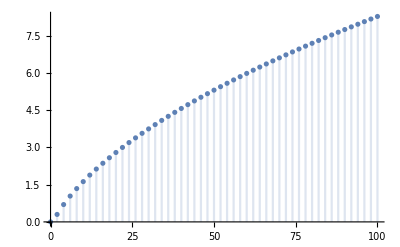

```mathematica
DiscretePlot[Log[10,PartitionsP[k]],{k,0,100,2}]
```

```mathematica
Inversions[{4,3,2,1}]
Inversions[{5,4,3,2,1}]
Inversions[{6,5,4,3,2,1}]
```

6

10

15

## tmp-0

```mathematica
ContourIntegrate[1/z,z∈Circle[]]
```

2 ⅈ π

## TEMP

## tmp

```mathematica
((1800-240) /7.)/20
```

11.1429

```mathematica
26/4.
```

6.5

```mathematica
(26-12) /3.
```

4.66667

```mathematica
(26 -22)
```

4

0.154431

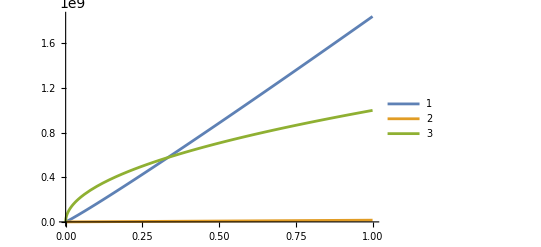

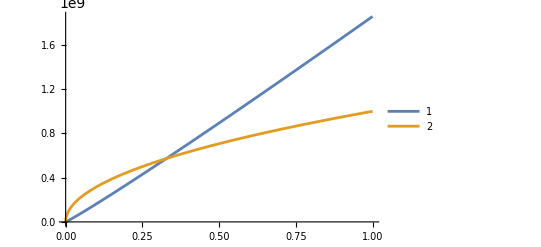

```mathematica
f[n_]:=n Log[n]
g[n_]:=((2 EulerGamma)-1)n
h[n_]:=10^5 √n
(2EulerGamma-1)//N
Plot[{f[k],g[k],h[k]},{k,1,10^8},PlotLegends->Automatic,AxesOrigin->{0,0}]
Plot[{f[k]+g[k],h[k]},{k,1,10^8},PlotLegends->Automatic,AxesOrigin->{0,0}]
```

```mathematica
Integrate[(1-12 y^2)/((1+4 y^2)^3)Log[Abs[Zeta[x+I y]]],{y,1/2,Infinity},{x,0,Infinity}]
```

$Aborted

```mathematica
RSolve[{a[0]==1,a[n]==a[n-1]+3},a[n],n]
```

{{a[n]→1+3 n}}

```mathematica
RSolve[{a[0]==2,a[1]==3,a[n]==a[n-1]a[n-2]},a[n],n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a[n]→2^(LucasL[n]/2) ⅇ^(1/2 Fibonacci[n] (-Log[2]+2 Log[3]))},{a[n]→ⅇ^(-1/2 ⅈ Fibonacci[n] (2 π-ⅈ Log[2]+2 ⅈ Log[3])+1/2 ⅈ (2 π-ⅈ Log[2]) LucasL[n])}}

```mathematica
f[n_]:=2^(LucasL[n]/2) ⅇ^(1/2 Fibonacci[n] (-Log[2]+2 Log[3]))
Table[{k,f[k]},{k,2,6}]//TableForm//N
```

2. | 6.
3. | 18.
4. | 108.
5. | 1944.
6. | 209952.

```mathematica
f[n_]:=(n^2+1)/(n^2+n)
```

```mathematica
Table[{k,f[k]},{k,1,6}]//TableForm//N
```

1. | 1.
2. | 0.833333
3. | 0.833333
4. | 0.85
5. | 0.866667
6. | 0.880952

```mathematica
27/5. 5/3 5/3
```

15.